Settings (phi = 0.0 rad):  tA=0.000 ps,  tB=1.552 ps,  tA'=3.104 ps,  tB'=10.865 ps  (T=12.417 ps)

GammaH=0.667 ps^-1,  GammaL=0.667 ps^-1,  ΔΓ=0.000 ps^-1,  C=1.

Window half-width sigmaWin = 0.3 ps

Selected counts:  AB=25600   A'B=7325   AB'=45   A'B'=15

Total pairs selected (across all four settings) = 32985

--- CHSH-like (unnormalized, picture probabilities) ---

E_raw(AB)=-0.2516  E_raw(A'B)=-0.0329  E_raw(AB')=-0.0005  E_raw(A'B')=0.0001

S_raw_empirical = -0.28506   (units of probability; not bounded by 2√2)

Set::write: Tag Times in _Raw S_fromPairs is Protected.

--- CHSH-like (unnormalized, averaging exact times of selected pairs) ---

S_raw_theory_from_selected_pairs = _Raw S_fromPairs

Set::write: Tag Times in _Raw S_markers is Protected.

S_raw_theory_at_markers = _Raw S_markers   (unnormalized; scales with survival factors)

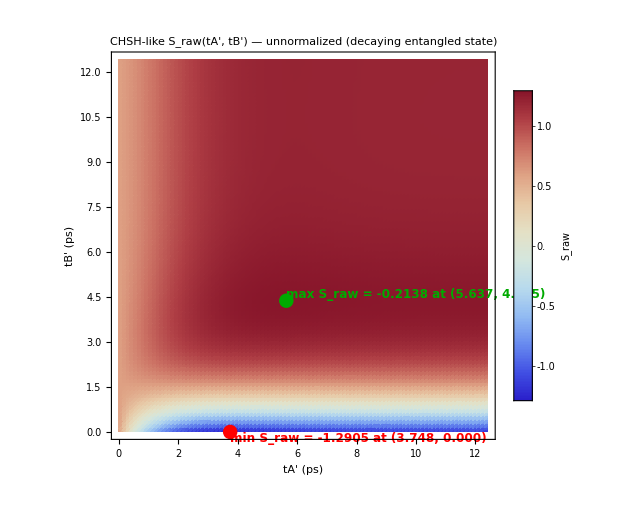

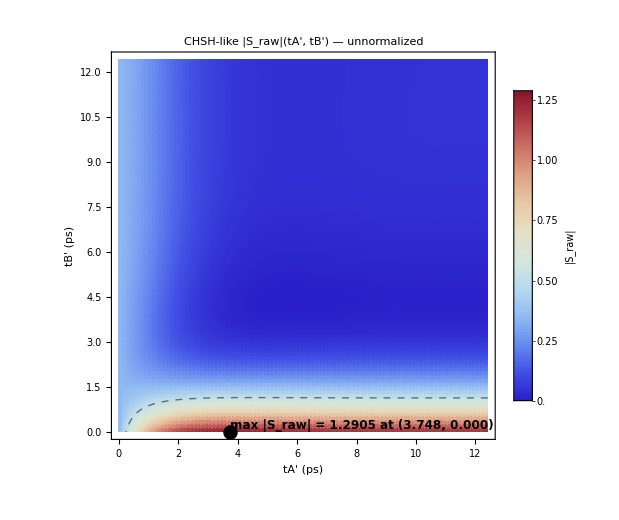

Max S_raw = -0.2138 at  tA'=5.637 ps,  tB'=4.375 ps

Min S_raw = -1.2905 at  tA'=3.748 ps,  tB'=0.000 ps

Max |S_raw| = 1.2905 at  tA'=3.748 ps,  tB'=0.000 ps

```mathematica
ClearAll["Global`*"];
Quiet@Needs["PlotLegends`"]; 

(*Mixing& decay parameters*)
deltaM=0.506;              (*ps^-1*)
tauAvg=1.5;                (*mean lifetime~1/GammaAvg,ps*)
GammaAvg=1/tauAvg;           (*ps^-1*)
dGamma=0.0;                (*ΔΓ=Γ_H-Γ_L (ps^-1)*)
GammaH=GammaAvg+dGamma/2;(*ps^-1*)
GammaL=GammaAvg-dGamma/2;(*ps^-1*)
Cmix=1.0;                (*C= |p|^2/|q|^2;C=1->CP conservation*)

T=2 Pi/deltaM;               (*oscillation period (ps)*)

(*Time-selection window& ensemble*)
sigmaWin=0.3;                (*ps,half-window*)
nPairs=1000000;            (*ensemble size*)

(*CHSH settings*)
phi=0.;
tWrap[t_]:=Mod[t,T];
tA=tWrap[phi/deltaM];
tB=tWrap[(phi+Pi/4)/deltaM];
tAp=tWrap[(phi+Pi/2)/deltaM];
tBp=tWrap[(phi-Pi/4)/deltaM];


sumExpHL[t1_?NumericQ,t2_?NumericQ]:=Exp[-(GammaH t1+GammaL t2)]+Exp[-(GammaL t1+GammaH t2)];

xi[t1_?NumericQ,t2_?NumericQ]:=Cos[deltaM (t1-t2)]/Cosh[dGamma (t1-t2)/2];

PBB[t1_?NumericQ,t2_?NumericQ]:=(Cmix/8)*sumExpHL[t1,t2]*(1-xi[t1,t2]);   (*B^0,B^0*)
PBbB[t1_?NumericQ,t2_?NumericQ]:=(1/8)*sumExpHL[t1,t2]*(1+xi[t1,t2]);   (*B^0,B̄^0*)
PBbBrev[t1_?NumericQ,t2_?NumericQ]:=(1/8)*sumExpHL[t1,t2]*(1+xi[t1,t2]);   (*B̄^0,B^0*)
PBbBb[t1_?NumericQ,t2_?NumericQ]:=(1/(8 Cmix))*sumExpHL[t1,t2]*(1-xi[t1,t2]);   (*B̄^0,B̄^0*)

(*Unnormalized correlation numerator at fixed times*)
ErawFromP[t1_?NumericQ,t2_?NumericQ]:=Module[{pp=PBB[t1,t2],pm=PBbB[t1,t2],mp=PBbBrev[t1,t2],mm=PBbBb[t1,t2]},pp+mm-pm-mp];

(*CHSH-like S built from unnormalized correlations*)
SmarkersRaw[tA_?NumericQ,tAp_?NumericQ,tB_?NumericQ,tBp_?NumericQ]:=ErawFromP[tA,tB]+ErawFromP[tAp,tB]+ErawFromP[tA,tBp]-ErawFromP[tAp,tBp];

(* Ensemble with proper H/L widths*)
SeedRandom[20250828];
expSample[gamma_]:=-Log[1-RandomReal[]]/gamma;

pairs=Table[If[RandomReal[]<1/2,<|"id"->i,"tL"->expSample[GammaL],"tR"->expSample[GammaH]|>,<|"id"->i,"tL"->expSample[GammaH],"tR"->expSample[GammaL]|>],{i,nPairs}];

Print["Settings (phi = ",NumberForm[phi,{3,1}]," rad):  tA=",NumberForm[tA,{5,3}]," ps,  tB=",NumberForm[tB,{5,3}]," ps,  tA'=",NumberForm[tAp,{5,3}]," ps,  tB'=",NumberForm[tBp,{5,3}]," ps  (T=",NumberForm[T,{5,3}]," ps)"];
Print["GammaH=",NumberForm[GammaH,{4,3}]," ps^-1,  GammaL=",NumberForm[GammaL,{4,3}]," ps^-1,  ΔΓ=",NumberForm[dGamma,{4,3}]," ps^-1,  C=",Cmix];
Print["Window half-width sigmaWin = ",sigmaWin," ps"];

(* Select pairs in the four windows*)
within[t_,c_]:=Abs[t-c]<=sigmaWin;
combos={{"AB",tA,tB},{"ApB",tAp,tB},{"ABp",tA,tBp},{"ApBp",tAp,tBp}};
buckets=<|"AB"->{},"ApB"->{},"ABp"->{},"ApBp"->{}|>;

Scan[Function[p,Module[{tL=p["tL"],tR=p["tR"],matches,best},matches=Select[combos,within[tL,#[[2]]]&&within[tR,#[[3]]]&];
If[matches=!={},best=First@SortBy[matches,Abs[tL-#[[2]]]+Abs[tR-#[[3]]]&];
buckets[best[[1]]]=Append[buckets[best[[1]]],{tL,tR}]];]],pairs];

qAB=Length[buckets["AB"]];
qApB=Length[buckets["ApB"]];
qABp=Length[buckets["ABp"]];
qApBp=Length[buckets["ApBp"]];
totalSelected=qAB+qApB+qABp+qApBp;

Print["Selected counts:  AB=",qAB,"   A'B=",qApB,"   AB'=",qABp,"   A'B'=",qApBp];
Print["Total pairs selected (across all four settings) = ",totalSelected];

(* CHSH from these pairs*)

(*Monte-Carlo estimator*)
sampleWeightedProduct[t1_?NumericQ,t2_?NumericQ]:=Module[{w={PBB[t1,t2],PBbB[t1,t2],PBbBrev[t1,t2],PBbBb[t1,t2]},z,ab},z=Total[w];
ab=Times@@RandomChoice[w->{{1,1},{1,-1},{-1,1},{-1,-1}}];
z*ab];

empiricalEraw[plist_List]:=If[Length[plist]==0,Missing["NoData"],Mean@(sampleWeightedProduct[#[[1]],#[[2]]]&/@plist)];

theoryEraw[plist_List]:=If[Length[plist]==0,Missing["NoData"],Mean@(ErawFromP[#[[1]],#[[2]]]&/@plist)];

EABempRaw=empiricalEraw[buckets["AB"]];
EApBempRaw=empiricalEraw[buckets["ApB"]];
EABpempRaw=empiricalEraw[buckets["ABp"]];
EApBpempRaw=empiricalEraw[buckets["ApBp"]];

EABthRaw=theoryEraw[buckets["AB"]];
EApBthRaw=theoryEraw[buckets["ApB"]];
EABpthRaw=theoryEraw[buckets["ABp"]];
EApBpthRaw=theoryEraw[buckets["ApBp"]];

haveEmpRaw=VectorQ[{EABempRaw,EApBempRaw,EABpempRaw,EApBpempRaw},NumericQ];
haveThRaw=VectorQ[{EABthRaw,EApBthRaw,EABpthRaw,EApBpthRaw},NumericQ];

If[haveEmpRaw,SempRaw=N[EABempRaw+EApBempRaw+EABpempRaw-EApBpempRaw,6];
Print["--- CHSH-like (unnormalized, picture probabilities) ---"];
Print["E_raw(AB)=",NumberForm[EABempRaw,{8,4}],"  E_raw(A'B)=",NumberForm[EApBempRaw,{8,4}],"  E_raw(AB')=",NumberForm[EABpempRaw,{8,4}],"  E_raw(A'B')=",NumberForm[EApBpempRaw,{8,4}]];
Print["S_raw_empirical = ",NumberForm[SempRaw,{10,5}],"   (units of probability; not bounded by 2√2)"],Print["Not enough data in one or more buckets to form S_raw_empirical."]];

If[haveThRaw,S_fromPairs_Raw=N[EABthRaw+EApBthRaw+EABpthRaw-EApBpthRaw,6];
Print["--- CHSH-like (unnormalized, averaging exact times of selected pairs) ---"];
Print["S_raw_theory_from_selected_pairs = ",NumberForm[S_fromPairs_Raw,{10,5}]],Print["Not enough data in one or more buckets to form S_raw_theory_from_selected_pairs."]];

S_markers_Raw=N[SmarkersRaw[tA,tAp,tB,tBp],10];
Print["S_raw_theory_at_markers = ",NumberForm[S_markers_Raw,{10,6}],"   (unnormalized; scales with survival factors)"];

(* 2D thermal heatmaps for S_raw and|S_raw| *)
sRange={0,T};
constraints=sRange[[1]]<=u<=sRange[[2]]&&sRange[[1]]<=v<=sRange[[2]];

(*Locate extrema over the domain*)
maxData=NMaximize[{SmarkersRaw[tA,u,tB,v],constraints},{u,v}];
minData=NMinimize[{SmarkersRaw[tA,u,tB,v],constraints},{u,v}];
absData=NMaximize[{Abs[SmarkersRaw[tA,u,tB,v]],constraints},{u,v}];

maxS=maxData[[1]];{uMax,vMax}={u,v}/. maxData[[2]];
minS=minData[[1]];{uMin,vMin}={u,v}/. minData[[2]];
maxAbsS=absData[[1]];{uAbs,vAbs}={u,v}/. absData[[2]];

(*Symmetric scale for S_raw;nonnegative for|S_raw|*)
sMin=-maxAbsS;sMax=maxAbsS;
absMin=0;absMax=maxAbsS;

(*Heatmap for S_raw*)
sHeat=DensityPlot[SmarkersRaw[tA,u,tB,v],{u,sRange[[1]],sRange[[2]]},{v,sRange[[1]],sRange[[2]]},ColorFunction->"ThermometerColors",ColorFunctionScaling->True,PlotRange->{sMin,sMax},Frame->True,FrameLabel->{"tA' (ps)","tB' (ps)"},PlotLabel->"CHSH-like S_raw(tA', tB') — unnormalized (decaying entangled state)",PlotPoints->100,MaxRecursion->2,ImageSize->520];

boundsS=ContourPlot[SmarkersRaw[tA,u,tB,v],{u,sRange[[1]],sRange[[2]]},{v,sRange[[1]],sRange[[2]]},Contours->{0},ContourStyle->{Directive[Black,Thick]},ContourShading->False,Frame->False,Axes->False,PlotPoints->100,MaxRecursion->2];

markersS=Graphics[{Darker[Green],PointSize[.02],Point[{uMax,vMax}],Inset[Style[Row[{"max S_raw = ",NumberForm[maxS,{7,4}]," at (",NumberForm[uMax,{5,3}],", ",NumberForm[vMax,{5,3}],")"}],12,Bold],{uMax,vMax},{Left,Bottom}],Red,PointSize[.02],Point[{uMin,vMin}],Inset[Style[Row[{"min S_raw = ",NumberForm[minS,{7,4}]," at (",NumberForm[uMin,{5,3}],", ",NumberForm[vMin,{5,3}],")"}],12,Bold],{uMin,vMin},{Left,Top}]}];

sHeatLegend=Legended[Show[sHeat,boundsS,markersS,PlotRange->All],Placed[BarLegend[{"ThermometerColors",{sMin,sMax}},LegendLabel->"S_raw"],Right]];
Print[sHeatLegend];

(*Heatmap for|S_raw|*)
absHeat=DensityPlot[Abs[SmarkersRaw[tA,u,tB,v]],{u,sRange[[1]],sRange[[2]]},{v,sRange[[1]],sRange[[2]]},ColorFunction->"ThermometerColors",ColorFunctionScaling->True,PlotRange->{absMin,absMax},Frame->True,FrameLabel->{"tA' (ps)","tB' (ps)"},PlotLabel->"CHSH-like |S_raw|(tA', tB') — unnormalized",PlotPoints->100,MaxRecursion->2,ImageSize->520];

boundsAbs=ContourPlot[Abs[SmarkersRaw[tA,u,tB,v]],{u,sRange[[1]],sRange[[2]]},{v,sRange[[1]],sRange[[2]]},Contours->{maxAbsS/2},ContourStyle->{Directive[Black,Thick,Dashed]},ContourShading->False,Frame->False,Axes->False,PlotPoints->100,MaxRecursion->2];

markerAbs=Graphics[{Black,PointSize[.02],Point[{uAbs,vAbs}],Inset[Style[Row[{"max |S_raw| = ",NumberForm[maxAbsS,{7,4}]," at (",NumberForm[uAbs,{5,3}],", ",NumberForm[vAbs,{5,3}],")"}],12,Bold],{uAbs,vAbs},{Left,Bottom}]}];

absHeatLegend=Legended[Show[absHeat,boundsAbs,markerAbs,PlotRange->All],Placed[BarLegend[{"ThermometerColors",{absMin,absMax}},LegendLabel->"|S_raw|"],Right]];
Print[absHeatLegend];

Print["Max S_raw = ",NumberForm[maxS,{8,4}]," at  tA'=",NumberForm[uMax,{5,3}]," ps,  tB'=",NumberForm[vMax,{5,3}]," ps"];
Print["Min S_raw = ",NumberForm[minS,{8,4}]," at  tA'=",NumberForm[uMin,{5,3}]," ps,  tB'=",NumberForm[vMin,{5,3}]," ps"];
Print["Max |S_raw| = ",NumberForm[maxAbsS,{8,4}]," at  tA'=",NumberForm[uAbs,{5,3}]," ps,  tB'=",NumberForm[vAbs,{5,3}]," ps"];
```